## Nibbling Analysis

```mathematica
Clear[buy,total]

buy[0]=1;      (* buy is the amont of [0,1] obtained by jth bid *)
total[0]=0; (* total share of [0,1] after j bids *)

buy[j_]:=buy[j]=a(1-total[j-1])
total[j_]:=total[j]=Collect[buy[j]+total[j-1],a]
```

```mathematica
{buy[1],buy[2],buy[3]}
{total[1],total[2],total[3]}
```

{a,(1-a) a,a (1-2 a+a^2)}

{a,2 a-a^2,3 a-3 a^2+a^3}

```mathematica
{buy[4],buy[5]}
{total[4],total[5]}
```

{a (1-3 a+3 a^2-a^3),a (1-4 a+6 a^2-4 a^3+a^4)}

{4 a-6 a^2+4 a^3-a^4,5 a-10 a^2+10 a^3-5 a^4+a^5}

```mathematica
Expand[1-(1-a)^4]
Expand[1-(1-a)^5]
```

4 a-6 a^2+4 a^3-a^4

5 a-10 a^2+10 a^3-5 a^4+a^5

Plot shows amount of α that was spent (in blue) and the amount of [0,1] that was captured (1-ⅇ^-α) (in magenta)

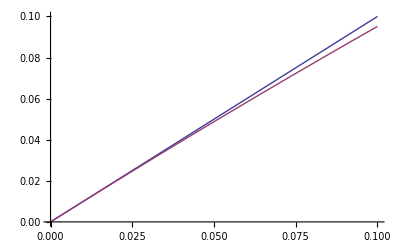

```mathematica
Plot[{α,1-ⅇ^-α},{α,0,0.1}]
```

The shortfall in the amount of p - value space captured by nibbling (ie, the cost of nibbling shown in blue) is then between α^2/2 and (α^2/2) (1- α/3).  Damn close to this lower bound.

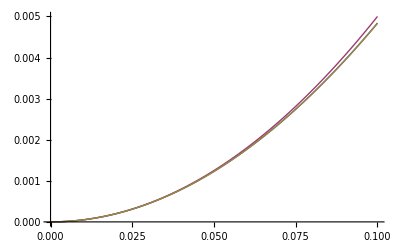

```mathematica
Plot[{α-(1-ⅇ^-α),α^2/2,α^2/2-α^3/6},{α,0,0.1}]
```

Said differently, in order to reject if a p-value is smaller than β, nibbling means that you have to spend α = log 1/(1-β) rather than just β.

```mathematica
Solve[1-ⅇ^-α==β,α,Reals]
```

{{α→ConditionalExpression[Log[1/(1-β)],β<1]}}

```mathematica
Series[Log[1/(1-β)],{β,0,3}]
```

β+β^2/2+β^3/3+O[β]^4